```mathematica
Fold[#+##&, Select[Range[1,999], Mod[#,3] == 0 || Mod[#,5] == 0 &]]
```

```mathematica
Range[1,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
cur = Select[Range[1,999], Mod[#,3]==0 || Mod[#,5] == 0 &]
```

```mathematica
Select[Range[1,999], EvenQ]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292,294,296,298,300,302,304,306,308,310,312,314,316,318,320,322,324,326,328,330,332,334,336,338,340,342,344,346,348,350,352,354,356,358,360,362,364,366,368,370,372,374,376,378,380,382,384,386,388,390,392,394,396,398,400,402,404,406,408,410,412,414,416,418,420,422,424,426,428,430,432,434,436,438,440,442,444,446,448,450,452,454,456,458,460,462,464,466,468,470,472,474,476,478,480,482,484,486,488,490,492,494,496,498,500,502,504,506,508,510,512,514,516,518,520,522,524,526,528,530,532,534,536,538,540,542,544,546,548,550,552,554,556,558,560,562,564,566,568,570,572,574,576,578,580,582,584,586,588,590,592,594,596,598,600,602,604,606,608,610,612,614,616,618,620,622,624,626,628,630,632,634,636,638,640,642,644,646,648,650,652,654,656,658,660,662,664,666,668,670,672,674,676,678,680,682,684,686,688,690,692,694,696,698,700,702,704,706,708,710,712,714,716,718,720,722,724,726,728,730,732,734,736,738,740,742,744,746,748,750,752,754,756,758,760,762,764,766,768,770,772,774,776,778,780,782,784,786,788,790,792,794,796,798,800,802,804,806,808,810,812,814,816,818,820,822,824,826,828,830,832,834,836,838,840,842,844,846,848,850,852,854,856,858,860,862,864,866,868,870,872,874,876,878,880,882,884,886,888,890,892,894,896,898,900,902,904,906,908,910,912,914,916,918,920,922,924,926,928,930,932,934,936,938,940,942,944,946,948,950,952,954,956,958,960,962,964,966,968,970,972,974,976,978,980,982,984,986,988,990,992,994,996,998}

```mathematica
Select[Range[1,999], (Mod[#,3]==0 ) || (Mod[##,5])];
```

```mathematica
Fold[#+##&,%]
```

Fold[#1+##1&,{}]

```mathematica
Fold[#1+#2&,%%]
```

Fold[#1+#2&,{}]

```mathematica
Fold[#+##&,{1,2,3,4,5}]
```

57

```mathematica
cur = Select[Range[1,999], (Mod[#,3]==0) || (Mod[#,5]==0) &]
```

{3,5,6,9,10,12,15,18,20,21,24,25,27,30,33,35,36,39,40,42,45,48,50,51,54,55,57,60,63,65,66,69,70,72,75,78,80,81,84,85,87,90,93,95,96,99,100,102,105,108,110,111,114,115,117,120,123,125,126,129,130,132,135,138,140,141,144,145,147,150,153,155,156,159,160,162,165,168,170,171,174,175,177,180,183,185,186,189,190,192,195,198,200,201,204,205,207,210,213,215,216,219,220,222,225,228,230,231,234,235,237,240,243,245,246,249,250,252,255,258,260,261,264,265,267,270,273,275,276,279,280,282,285,288,290,291,294,295,297,300,303,305,306,309,310,312,315,318,320,321,324,325,327,330,333,335,336,339,340,342,345,348,350,351,354,355,357,360,363,365,366,369,370,372,375,378,380,381,384,385,387,390,393,395,396,399,400,402,405,408,410,411,414,415,417,420,423,425,426,429,430,432,435,438,440,441,444,445,447,450,453,455,456,459,460,462,465,468,470,471,474,475,477,480,483,485,486,489,490,492,495,498,500,501,504,505,507,510,513,515,516,519,520,522,525,528,530,531,534,535,537,540,543,545,546,549,550,552,555,558,560,561,564,565,567,570,573,575,576,579,580,582,585,588,590,591,594,595,597,600,603,605,606,609,610,612,615,618,620,621,624,625,627,630,633,635,636,639,640,642,645,648,650,651,654,655,657,660,663,665,666,669,670,672,675,678,680,681,684,685,687,690,693,695,696,699,700,702,705,708,710,711,714,715,717,720,723,725,726,729,730,732,735,738,740,741,744,745,747,750,753,755,756,759,760,762,765,768,770,771,774,775,777,780,783,785,786,789,790,792,795,798,800,801,804,805,807,810,813,815,816,819,820,822,825,828,830,831,834,835,837,840,843,845,846,849,850,852,855,858,860,861,864,865,867,870,873,875,876,879,880,882,885,888,890,891,894,895,897,900,903,905,906,909,910,912,915,918,920,921,924,925,927,930,933,935,936,939,940,942,945,948,950,951,954,955,957,960,963,965,966,969,970,972,975,978,980,981,984,985,987,990,993,995,996,999}

```mathematica
Fold[#+##&,%]
```

921176032067976453919082136544297159380401495792078831771500894482219184279715994649027641371351380976703666967458008993700910945902189564611

```mathematica
Fold[Plus,cur]
```

233168

```mathematica
Times[3,4]
```

12

```mathematica
Fibonacci[10]
```

55

```mathematica
Fibonacci[10,x]
```

5 x+20 x^3+21 x^5+8 x^7+x^9

```mathematica
Fibonacci[Range[1,10]]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
TakeWhile[{i,1,10},# < 5]
```

{}

```mathematica
TakeWhile[{i, 1,10}, # < 5 &]
```

{}

```mathematica
TakeWhile[[1,10], #< 5 &]
```

```mathematica
TakeWhile[Range[1,10], # < 5 &]
```

{1,2,3,4}

```mathematica
Fold[Plus, Select[Fibonacci, EvenQ]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[Fibonacci, EvenQ].

EvenQ+Fibonacci

```mathematica
Fibonacci1
```

Fibonacci1

```mathematica
FibonacciList
```

FibonacciList

```mathematica
psqrQ[x] = tmp = Sqrt[x] ; Ceiling[tmp] == Floor[tmp]
```

Ceiling[√x]==Floor[√x]

```mathematica
psqrQ[100]
```

psqrQ[100]

```mathematica
psqrQ[4]
```

psqrQ[4]

```mathematica
psqrQ[4] //N
```

psqrQ[4.]

```mathematica
N[psqrQ[4]]
```

psqrQ[4.]

```mathematica
psqrQ[x] := tmp = Sqrt[x] ; Ceiling[tmp] == Floor[tmp]
```

Ceiling[√x]==Floor[√x]

```mathematica
psqrQ[100]
```

psqrQ[100]

```mathematica
psqrQ[x_] = Ceiling[tmp] == Floor[tmp] /. tmp -> Sqrt[x]
```

Ceiling[√x]==Floor[√x]

```mathematica
psqrQ[100]
```

True

```mathematica
psqrQ[10]
```

False

```mathematica
x > y > z > 0
```

x>y>z>0

```mathematica
Table[x+y, x= {1,2,3}, y = {2,3,4}]
```

{{{3,5,7},{3,5,7},{3,5,7}},{{3,5,7},{3,5,7},{3,5,7}},{{3,5,7},{3,5,7},{3,5,7}}}

```mathematica
Table[x+y, {x,1,2,3,4}, {y,2,3,4}]
```

Table::itform: Argument {x, 1, 2, 3, 4} at position 2 does not have the correct form for an iterator.

Table[x+y,{x,1,2,3,4},{y,2,3,4}]

```mathematica
Table[x*y, {x,1,10}, {y,10,2,-1}]
```

{{10,9,8,7,6,5,4,3,2},{20,18,16,14,12,10,8,6,4},{30,27,24,21,18,15,12,9,6},{40,36,32,28,24,20,16,12,8},{50,45,40,35,30,25,20,15,10},{60,54,48,42,36,30,24,18,12},{70,63,56,49,42,35,28,21,14},{80,72,64,56,48,40,32,24,16},{90,81,72,63,54,45,36,27,18},{100,90,80,70,60,50,40,30,20}}

```mathematica
x > y> z > 0
```

{1,2,3}>{2,3,4}>z>0

```mathematica
x =.;y=.;z=.
```

```mathematica
x > y > z >0
```

x>y>z>0

```mathematica
#*#&/@Range[1,10]
```

{1,4,9,16,25,36,49,64,81,100}

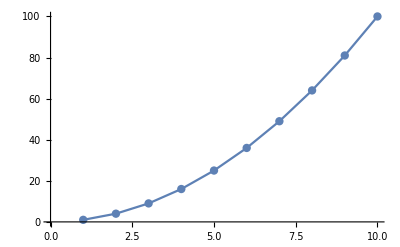

```mathematica
ListLinePlot[{1,4,9,16,25,36,49,64,81,100},Mesh->All]
```

```mathematica
NearestFunction[Range[1,10,2]]
```

NearestFunction[{1,3,5,7,9}]

```mathematica
%[10]
```

NearestFunction[{1,3,5,7,9}][10]

```mathematica
Nearest[Range[1,10,2]]
```

NearestFunction[{1, <>}]

```mathematica
%[1]
```

{1}

```mathematica
%[5]
```

{1}[5]

```mathematica
%%%[5]
```

{5}

```mathematica
Select[Mod[#,3]==0&]
```

Select[Mod[#1,3]==0&]

```mathematica
%[Range[1,100]]
```

{3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99}